Clifford Decomposition

The Principle and Algorithmpaclet:QuantumMob/Q3/tutorial/CliffordDecomposition#1645067439 | A Gray-Code Decomposition: Comparisonpaclet:QuantumMob/Q3/tutorial/CliffordDecomposition#1062129407
Demonstrationpaclet:QuantumMob/Q3/tutorial/CliffordDecomposition#1661615730 |

See also Section 6.3 of the Quantum Workbook (2022)https://doi.org/10.1007/978-3-030-91214-7.

Any Clifford unitary operator may be generated by a product of Hadamard gate, quadrant phase gate, and CNOT gate. Here, we demonstrate how to find those factors for a given Clifford unitary operator. The method uses the algorithm in van den Berg (2021). Previously, it was based on Gottesman's theorem in Gottesman (1998). While the latter provides a more compact set of (a bit higher-level) gates, the former is faster and easier to trace the changes in the sign of Pauli strings.

GottesmanMatrixpaclet:QuantumMob/Q3/ref/GottesmanMatrixQuantumMob Package Symbol | The binary symplectic matrix corresponding to a Clifford operator.
FromGottesmanMatrixpaclet:QuantumMob/Q3/ref/FromGottesmanMatrixQuantumMob Package Symbol | The Clifford operator corresponding to a Gottesman matrix.
GottesmanVectorpaclet:QuantumMob/Q3/ref/GottesmanVectorQuantumMob Package Symbol | The binary vector corresponding to a Pauli operator. 
FromGottesmanVectorpaclet:QuantumMob/Q3/ref/FromGottesmanVectorQuantumMob Package Symbol | The Pauli operator correspoinding to a Gottesman vector.
CliffordFactorpaclet:QuantumMob/Q3/ref/CliffordFactorQuantumMob Package Symbol | Decompose a Clifford unitary operator into a product of the elementary Clifford gates.

Functions related to the Clifford decomposition.

The Principle and Algorithm

Let Ĉ be an n-qubit Clifford unitary operator. Note that one can test efficiently if an operator is a Clifford unitary operator or not (see CliffordQ).

1. If necessary, transform Ĉ to another n-qubit unitary operator Û so that

Û(X̂⊗Î⊗…⊗Î)(Û)^†=Ẑ⊗Â

Û(Ẑ⊗Î⊗…⊗Î)(Û)^†=X̂⊗B̂ ,

where Â and B̂ are (n-1)-qubit Pauli operators. Note that one can always do this by rearranging qubits and/or applying a single-qubit Clifford operator (see Problem 6.6 of the Quantum Workbookhttps://doi.org/10.1007/978-3-030-91214-7)

2. Construct an (n-1)-qubit Clifford operator from Û by

V̂ y:=Σ_(x=0)^(2^n-1)x(0⊗x)Û(0⊗y)

for y=0,1,2,…,2^n-1. In effect, V̂takes the component of Û corresponding to 1 on the first qubit. Putting it another way, the matrix representation V of V̂ is just the upper-left block of the matrix representation U of Û as shown in Figure 1.

-Graphics-

Figure 1. The block structure of the matrix representation U of the Clifford unitary operator Û.

The crucial point is that derived from Û, the new operator V̂ is an element of the (n-1)-qubit Clifford group 𝒞(n-1) (see Problem 6.7 of the Quantum Workbook). In other words, the conjugation by V̂ preserves the (n-1)-qubit Pauli group 𝒫(n-1).

3. Express the Clifford unitary operator Û in terms of (n-1)-qubit Pauli operators Â and B̂ and Clifford unitary operator V̂ obtained in steps 1 and 2  using the quantum circuit shown in Figure 2. The detailed proof that the quantum circuit in Figure 2 reproduces Û is given in the original paper Gottesman (1998) and in Section 6.3 of the Quantum Workbook.

(... figure ...)

Figure 2. Quantum circuit decomposing a Clifford operation.

4. Now, apply the above steps 1 through 3 to the (n-1)-qubit Clifford unitary operator V̂.

Demonstration

Make sure that the package is loaded. Note that the Q3 package is also loaded automatically.

```mathematica
Needs["QuantumMob`Q3`"]
```

Choose symbol, say, S to denote the qubits.

```mathematica
Let[Qubit,S]
```

Start with a small number of qubits.

```mathematica
$n=3;
ss=S[Range@$n,$]
```

{S_(,,1),S_(,,2),S_(,,3)}

Now, choose a Clifford unitary operator. You can construct one by applying generators, that is, the Hadamard (H), quadrant (S), and CNOT gates. Here, we do it by choosing a Gottesman matrix.

Gottesman matrices are elements of the binary symplectic group, that is, a symplectic group  over the field of binary numbers.

```mathematica
gts=First@BinarySymplecticGroupElements[ss,{2}];
gts//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0)

Take a look at the corresponding Clifford operator and its matrix representation in the standard computational basis.

```mathematica
mat=FromGottesmanMatrix[gts];
mat//ArrayShort
```

(1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | …
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | …
1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | …
-1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | …
… | … | … | … | …)

Get the elementary Clifford gates that reconstruct the Clifford operator. Note that function CliffordFactorpaclet:QuantumMob/Q3/ref/CliffordFactorQuantumMob Package Symbol takes a Gottesman matrix as its input (not the actually Clifford unitary operator or matrix).

```mathematica
gates=CliffordFactor[gts,ss]
```

{SWAP[S_(,,1),S_(,,3)],{S_(,,1)^(,,H)},CNOT[{S_(,,1)→1},{S_(,,3)}],{S_(,,1)^(,,H)},{S_(,,3)^(,,H)},SWAP[S_(,,2),S_(,,3)],{S_(,,2)^(,,H)},CNOT[{S_(,,2)→1},{S_(,,3)}],{S_(,,2)^(,,H)}}

Show the elementary gates in the quantum circuit model.

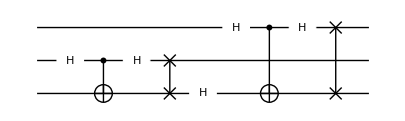

```mathematica
qc=QuantumCircuit[Sequence@@Reverse@gates]
```

Check whether the quantum circuit indeed reconstruct the Clifford unitary operator.

```mathematica
Matrix[qc]-mat//ArrayShort
```

(0 | 0 | 0 | 0 | …
0 | 0 | 0 | 0 | …
0 | 0 | 0 | 0 | …
0 | 0 | 0 | 0 | …
… | … | … | … | …)

```mathematica
Matrix[qc]-mat//ArrayZeroQ
```

True

A Gray-Code Decomposition: Comparison

It is interesting and heuristic to compare the above Clifford decomposition with the more common gray-code-based decomposition.

Use the same symbol S to denote the qubits.

```mathematica
Let[Qubit,S]
```

Consider the same number of qubits.

```mathematica
$n=3;
ss=S[Range@$n,$]
```

{S_(,,1),S_(,,2),S_(,,3)}

Consider again the same Gottesman matrix as in the above example.

```mathematica
gts=First@BinarySymplecticGroupElements[ss,{2}];
gts//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0)

This is the same Clifford unitary operator corresponding to the Gottesman matrix.

```mathematica
mat=FromGottesmanMatrix[gts];
mat//ArrayShort
```

(1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | …
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | …
1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | …
-1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | …
… | … | … | … | …)

Decompose the unitary matrix into two-level matrices. Here, we convert the matrix into numerically approximate form to avoid unnecessary complexity to deal with exact numbers. Note that the number of required two-level matrices is already over 25.

```mathematica
gvs=GivensFactor[N@mat,ss];
Length[gvs]
```

29

Check some of the elements.

```mathematica
ArrayShort/@Matrix@gvs[[;;5]]
```

{(1. | 0 | 0 | 0 | …
0 | 1. | 0 | 0 | …
0 | 0 | 1. | 0 | …
0 | 0 | 0 | 1. | …
… | … | … | … | …),(1. | 0 | 0 | 0 | …
0 | 1. | 0 | 0 | …
0 | 0 | 1. | 0 | …
0 | 0 | 0 | 1. | …
… | … | … | … | …),(1. | 0 | 0 | 0 | …
0 | 1. | 0 | 0 | …
0 | 0 | 1. | 0 | …
0 | 0 | 0 | 1. | …
… | … | … | … | …),(1. | 0 | 0 | 0 | …
0 | 1. | 0 | 0 | …
0 | 0 | 1. | 0 | …
0 | 0 | 0 | 1. | …
… | … | … | … | …),(1. | 0 | 0 | 0 | …
0 | 1. | 0 | 0 | …
0 | 0 | 1. | 0 | …
0 | 0 | 0 | 1. | …
… | … | … | … | …)}

Convert the two-level unitary matrices to quantum circuit elements consists of controlled-unitary and CNOT gates.

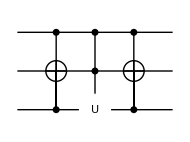
{1.,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
elm=Expand/@gvs;
elm[[;;5]]
```

Note that there are about 60 quantum circuit elements. This is in stark contrast with the Clifford decomposition shown in the above example, which had only 7 elementary gates.

```mathematica
elm=Flatten[Expand/@gvs,1,QuantumCircuit];
elm[[;;5]]
```

{1.,ControlledGate[{S_(,,1)→1,S_(,,2)→1},0.707107-(0.+0.707107 ⅈ) S_(,,3)^(,,Y),Label→U],CNOT[{S_(,,1)→1,S_(,,3)→1},{S_(,,2)}],ControlledGate[{S_(,,1)→1,S_(,,2)→1},0.57735-(0.+0.816497 ⅈ) S_(,,3)^(,,Y),Label→U],CNOT[{S_(,,1)→1,S_(,,3)→1},{S_(,,2)}]}

```mathematica
Length[elm]
```

61

Take a look at the first several elements.

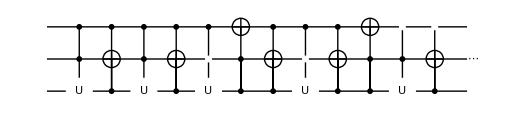

```mathematica
new=QuantumCircuit[Sequence@@Take[Reverse@elm,12],
{Ket[S[2]->1],"Label"->"⋯"}]
```

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪The Pauli and Clifford Groups
▪Stabilizer Formalism
▪Quantum Error-Correction Codes
▪Quantum Information Systems with Q3

| Related Links
▪E. van den Berg (2021)https://doi.org/10.1109/qce52317.2021.00021, "A simple method for sampling random Clifford operators" in 2021 IEEE International Conference on Quantum Computing and Engineering (QCE).
▪D. Gottesman, Physical Review A 54, 1862 (1996)https://doi.org/10.1103%2Fphysreva.54.1862, “Class of quantum error- correcting codes saturating the quantum Hamming bound.”
▪D. Gottesman (1997)https://arxiv.org/abs/quant-ph/9705052, Stabilizer Codes and Quantum Error Correction (Ph.D. Thesis, California Institute of Technology, 1997).
▪D. Gottesman, Physical Review A 57, 127 (1998)https://doi.org/10.1103/PhysRevA.57.127, “Theory of fault-tolerant quantum computation.”
▪E. Hostens, J. Dehaene, and B. De Moor, Physical Review A 71, 042315 (2005)https://doi.org/10.1103/PhysRevA.71.042315, "Stabilizer states and Clifford operations for systems of arbitrary dimensions and modular arithmetic."
▪S. Aaronson and D. Gottesman, Physical Review A 70 (5) (2004)https://doi.org/10.1103/physreva.70.052328, “Improved simulation of stabilizer circuits.”
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).